```mathematica
STAT 333 Project 6
```

```mathematica
Iris Zhang
```

```mathematica
Problem 1
```

```mathematica
Obtain 0.950level confidence bands and prediction bands for the regression problem considered in Mathematica Experiement 8.16. Test the lumberjack's hypothesis.
```

```mathematica
V = {114,96,100,110,112,108,100,132,118,100,94,144,110,134,106,102,138,102,102,100,106,118,106,98,132};
Vmean=Mean[V];
```

```mathematica
C2 ={22.09,7.29,12.25,6.25,16,12.96,7.29,30.25,25,6.76,6.25,36,14.44,33.64,15.21,7.84,33.64,12.25,12.96,6.25,12.25,22.09,12.96,6.25,33.64};
C2mean =Mean[C2];
```

```mathematica
size=Length[C2];
```

```mathematica
Sxx= ∑_(j=1)^size (C2[[j]]-C2mean)^2;
```

```mathematica
Subscript[t, α/2]= 2.069;
```

```mathematica
sigma  =(∑_(j=1)^size (V[[j]]-(89.06851927315793+1.3484058623419801*C2[[j]]))^2)/(size-2);
```

```mathematica
data = Table[{C2[[i]],V[[i]]},{i,25}];
Fit[data,{1,x},x]
```

89.0685+1.34841 x

```mathematica
LinearModelFit[data,x,x]
```

FittedModel[89.0685+1.34841 x]

```mathematica
LinearModelFit[data,x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 89.0685 | 1.5985 | 55.7201 | 4.81472×10^-26
x | 1.34841 | 0.0832075 | 16.2053 | 4.48225×10^-14

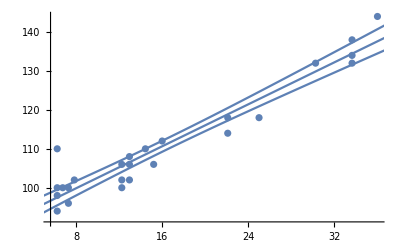

```mathematica
f[x_] = 89.06851927315793+1.3484058623419801x;
p1 = ListPlot[data];
p2  = Plot [f[x],{x,4,49}];
f1[x_] = 89.06851927315793+1.3484058623419801x+Quantile[StudentTDistribution[size-2],0.95]*Sqrt[sigma*((1/size)+(x-C2mean)^2/Sxx)];
f2[x_] = 89.06851927315793+1.3484058623419801x-Quantile[StudentTDistribution[size-2],0.95]*Sqrt[sigma*((1/size)+(x-C2mean)^2/Sxx)];
p3 = Plot [f1[x],{x,4,49}];
p4= Plot [f2[x],{x,4,49}];
Show[p1,p2,p3,p4]
```

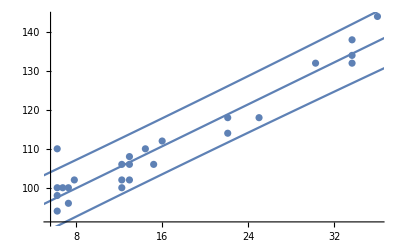

```mathematica
f3[x_]= 89.06851927315793+1.3484058623419801x+Quantile[StudentTDistribution[size-2],0.95]*Sqrt[sigma*(1+(1/size)+(x-C2mean)^2/Sxx)];
f4[x_] = 89.06851927315793+1.3484058623419801x-Quantile[StudentTDistribution[size-2],0.95]*Sqrt[sigma*(1+(1/size)+(x-C2mean)^2/Sxx)];
p5 = Plot [f3[x],{x,4,49}];
p6= Plot [f4[x],{x,4,49}];
Show[p1,p2,p5,p6]
```

We need to test that β_0 = 100 and β_1 =2/3

```mathematica
f5[x_]=100+2/3x;
p7= Plot [f5[x],{x,4,49}];
```

```mathematica
Sigma  =(∑_(j=1)^size (V[[j]]-(100+2/3*C2[[j]]))^2)/(size-2);
```

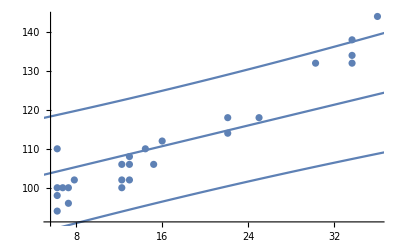

```mathematica
f6[x_]=100+2/3x+Quantile[StudentTDistribution[size-2],0.95]*Sqrt[Sigma*(1+(1/size)+(x-C2mean)^2/Sxx)];
f7[x_] = 100+2/3x-Quantile[StudentTDistribution[size-2],0.95]*Sqrt[Sigma*(1+(1/size)+(x-C2mean)^2/Sxx)];
p8 = Plot [f6[x],{x,4,49}];
p9= Plot [f7[x],{x,4,49}];
Show[p1,p7,p8,p9]
```

From above graph, we can see that approximately 95% of the data points are between the band.

```mathematica
Mean[V-2/3*C2]
```

100.298

```mathematica
Mean[(V-100)/C2]
```

0.451651

From above calculation, we can also find that β_0 is approximately 100 and β_1 is approximately 2/3.

```mathematica
Problem 2
```

```mathematica
Test the assumption of normality for the POTATOES regression problem from Table 8.51. Find the residuals first.
```

```mathematica
potatoes={
{1.064,9.5},{1.064,10.5},
{1.068,10.5}, {1.068,12.5},
{1.072, 11.5},{1.072, 11.5},{1.072, 11.5},{1.072, 11.5},{1.072, 11.5},
{1.072, 12.5},{1.072, 12.5},{1.072, 12.5},{1.072, 12.5},{1.072, 12.5},
{1.072, 13.5},
{1.076, 11.5}, 
{1.076, 12.5},{1.076, 12.5},
{1.076, 13.5},{1.076, 13.5},
{1.080, 12.5},{1.080, 12.5},{1.080, 12.5},
{1.080, 13.5},
{1.080, 14.5},{1.080,14.5},{1.080, 14.5},{1.080, 14.5},{1.080, 14.5},{1.080, 14.5},
{1.084, 12.5},
{1.084, 13.5},{1.084, 13.5},{1.084, 13.5},{1.084, 13.5},{1.084,
13.5},{1.084, 13.5},{1.084, 13.5},{1.084, 13.5},{1.084, 13.5},
{1.084, 14.5},{1.084,14.5},{1.084, 14.5},{1.084, 14.5},{1.084, 
14.5},{1.084, 14.5},{1.084, 14.5},{1.084,14.5},{1.084, 14.5}, 
{1.084, 15.5},{1.084, 15.5},{1.084, 15.5},
{1.088, 14.5},{1.088, 14.5},{1.088, 14.5},{1.088, 14.5},{1.088, 14.5},
{1.088,14.5},{1.088, 14.5},{1.088, 14.5},{1.088, 14.5},{1.088, 14.5},
{1.088, 14.5},
{1.088, 15.5},{1.088, 15.5},{1.088, 15.5},{1.088, 15.5},{1.088, 15.5},
{1.088,15.5},{1.088, 15.5},{1.088, 15.5},{1.088, 15.5},{1.088, 15.5},
{1.088, 15.5},{1.088,15.5},{1.088, 15.5},{1.088, 15.5},{1.088, 15.5},
{1.088, 15.5},{1.088, 15.5},{1.088,15.5},{1.088, 15.5},
{1.088, 16.5},{1.088, 16.5},{1.088, 16.5},{1.088, 16.5},{1.088,16.5},
{1.088, 16.5},{1.088, 16.5},{1.088, 16.5},{1.088, 16.5},{1.088, 16.5},
{1.088, 16.5},
{1.088, 17.5},{1.088, 17.5},
{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},
{1.092,15.5},{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},
{1.092, 15.5},{1.092,15.5},{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},
{1.092, 15.5},{1.092, 15.5},{1.092, 15.5},
{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},
{1.092,16.5},{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},
{1.092, 16.5},{1.092,16.5},{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},
{1.092, 16.5},{1.092, 16.5},{1.092,16.5},{1.092, 16.5},{1.092, 16.5},
{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},{1.092,16.5},{1.092, 16.5},
{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},{1.092, 16.5},{1.092,16.5},
{1.092, 17.5},{1.092, 17.5},{1.092, 17.5},{1.092, 17.5},{1.092, 17.5},
{1.092,17.5},{1.092, 17.5},{1.092, 17.5},{1.092, 17.5},{1.092, 17.5},
{1.092, 17.5},
{1.092, 18.5},{1.092, 18.5},
{1.096, 15.5},{1.096, 15.5},{1.096, 15.5},{1.096, 15.5},{1.096, 15.5},
{1.096, 15.5},
{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},
{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},
{1.096, 16.5},{1.096,16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},
{1.096, 16.5},{1.096, 16.5},{1.096,16.5},{1.096, 16.5},{1.096, 16.5},
{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096,16.5},{1.096, 16.5},
{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096,16.5},
{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},
{1.096,16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},{1.096, 16.5},
{1.096, 16.5},{1.096,16.5},{1.096, 16.5},  
{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},
{1.096,17.5},{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},
{1.096, 17.5},{1.096,17.5},{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},
{1.096, 17.5},{1.096, 17.5},{1.096,17.5},{1.096, 17.5},{1.096, 17.5},
{1.096, 17.5},{1.096, 17.5},{1.096, 17.5},{1.096,17.5},{1.096, 17.5},
{1.096, 17.5},{1.096, 17.5},{1.096, 17.5}, {1.096, 17.5},{1.096,17.5},
{1.096, 17.5},{1.096, 17.5},{1.096, 17.5}, 
{1.096, 18.5},{1.096, 18.5},{1.096, 18.5},{1.096, 18.5},
{1.100, 16.5},{1.100, 16.5},{1.100, 16.5},{1.100, 16.5},{1.100, 16.5},
{1.100,16.5},{1.100, 16.5},{1.100, 16.5},{1.100, 16.5},{1.100, 16.5},
{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100,17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 17.5},{1.100,17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 17.5},{1.100, 17.5},{1.100,17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100,17.5},{1.100, 17.5},
{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100,17.5},
{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100,17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 17.5},{1.100,17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 17.5},{1.100, 17.5},{1.100,17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},{1.100, 17.5},
{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},
{1.100,18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},
{1.100, 18.5},{1.100,18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},
{1.100, 18.5},{1.100, 18.5},{1.100,18.5},{1.100, 18.5},{1.100, 18.5},
{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100,18.5},{1.100, 18.5},
{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100,18.5},
{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},
{1.100,18.5},{1.100, 18.5},{1.100, 18.5},{1.100, 18.5},
{1.100,19.5},{1.100,19.5},
{1.104, 20.5},
{1.108, 20.5},{1.108, 20.5},{1.108, 20.5},{1.108, 20.5},{1.108, 20.5},
{1.108, 20.5},
{1.112, 20.5},{1.112, 20.5},{1.112, 20.5},{1.112, 20.5},{1.112, 20.5},
{1.112,20.5},{1.112, 20.5},{1.112, 20.5},{1.112, 20.5},{1.112, 20.5},
{1.112, 20.5},{1.112,20.5},{1.112, 20.5},{1.112, 20.5},{1.112, 20.5},
{1.112, 20.5},{1.112, 20.5},{1.112,20.5},{1.112, 20.5},{1.112, 20.5},
{1.112, 20.5},{1.112, 20.5},
{1.116, 20.5},{1.116, 20.5},{1.116, 20.5},{1.116, 20.5},{1.116, 20.5},
{1.116,20.5},{1.116, 20.5},{1.116, 20.5},{1.116, 20.5},
{1.116, 21.5},{1.116, 21.5},{1.116, 21.5},{1.116, 21.5},{1.116, 21.5},
{1.116,21.5},{1.116, 21.5},{1.116, 21.5},{1.116, 21.5},{1.116, 21.5},
{1.116, 21.5},
{1.116, 22.5},
{1.120, 20.5},
{1.120, 21.5},{1.120, 21.5},{1.120, 21.5},
{1.120, 22.5},
{1.124, 22.5},{1.124, 22.5},{1.124, 22.5},{1.124, 22.5},
{1.124, 23.5},
{1.128, 22.5},{1.140, 25.5}};
```

```mathematica
potatofit= LinearModelFit[potatoes,x,x]
```

FittedModel[-208.146+205.466 x]

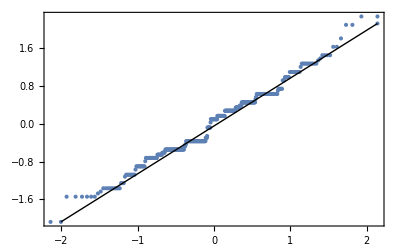

```mathematica
residual=potatofit["FitResiduals"];
QuantilePlot[residual]
```

From above we can see that the Q-Q plot of the residuals is an approximately straight line, which indicates that the residuals are approximately normally distributed.

```mathematica
Problem 3
```

```mathematica
Construct confidence intervals for the variance σ^2 of the N(μ,σ^2), based on a random sample of size n and assuming that the mean μ is known.
```

We know that X_1,X_2,... , X_n∼N(μ,σ^2). Then, 1/σ^2∑_(i=1)^n (X_i-μ)^2∼χ^2(n). But, 1/σ^2∑_(i=1)^n (X_i-X̄)^2∼χ^2(n-1)
Suppose μ is known, then χ_α^2(n) = Q(1-α;n) and P[1/σ^2∑_(i=1)^n (X_i-μ)^2⩽χ_(1-α/2)^2(n) ]=α/2 and P[χ_(α/2)^2(n) ≤1/σ^2∑_(i=1)^n (X_i-μ)^2]=α/2 so that we have P[1/(χ_(α/2)^2(n))∑_(i=1)^n (X_i-μ)^2≤σ^2≤1/(χ_(1-α/2)^2(n))∑_(i=1)^n (X_i-μ)^2] =1-α. Therefore, the (1-α)*100% confidence interval for σ^2is [ (∑_(i=1)^n (X_i-μ)^2)/(χ_(α/2)^2(n)), (∑_(i=1)^n (X_i-μ)^2)/(χ_(1-α/2)^2(n))]